```mathematica
ClearAll[x,y,z,flukaDataIP]
```

```mathematica
flukaData=Import["/home/hovanes/klcps_31b.bnn.lis.table.csv_swapped","CSV"]
```

{{0.0125,-3.11978,0.25,38.0905},{0.0125,-3.11978,0.75,72.645},{0.0125,-3.11978,1.25,126.035},{0.0125,-3.11978,1.75,179.89},{0.0125,-3.11978,2.25,254.1},{0.0125,-3.11978,2.75,354.11},{0.0125,-3.11978,3.25,411.005},{0.0125,-3.11978,3.75,504.25},{0.0125,-3.11978,4.25,575.85},6497262,{5.9875,-3.1634,89.75,0.000292525},{5.9875,-3.1634,90.25,0.00150975},{5.9875,-3.1634,90.75,0.00231685},{5.9875,-3.1634,91.25,0.0016567},{5.9875,-3.1634,91.75,0.0043239},{5.9875,-3.1634,92.25,0.0013032},{5.9875,-3.1634,92.75,0.00092605},{5.9875,-3.1634,93.25,0.000234535},{5.9875,-3.1634,93.75,0.0018861}}
 |  |  |  |

```mathematica
flukaDataIP=Interpolation[flukaData,InterpolationOrder->5]
```

InterpolatingFunction[{{0.0125, 5.9875}, {-5.21417, 1.02538}, {0.25, 93.75}}, <>]

InterpolatingFunction::dmval: Input value {0.26,-5.23554,2.00629} lies outside the range of data in the interpolating function. Extrapolation will be used.

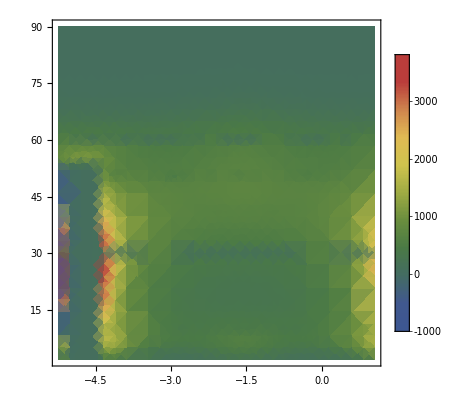

```mathematica
DensityPlot[flukaDataIP[0.26,y,z], {y,-5*Pi/3,+Pi/3}, {z,2, 90},PlotRange->Full,ColorFunction->{"DarkRainbow"},PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,Identity}]
```

InterpolatingFunction::dmval: Input value {0.000428571,-(5 π)/3,2.00629} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.428571,-(5 π)/3,8.28571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

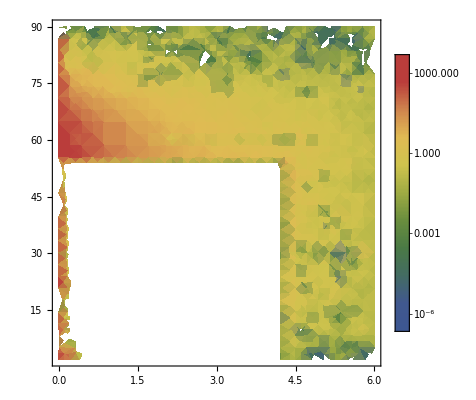

```mathematica
DensityPlot[flukaDataIP[x,-5*Pi/3,z], {x,0,6}, {z,2, 90},PlotRange->Full,ColorFunction->{"DarkRainbow"},PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"}]
```

```mathematica
Export["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/klcps_31b_swapped.m" , flukaDataIP]
```

/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/klcps_31b_swapped.m